# Spin Temperature

```mathematica
Jz=1/2 {{1,0},{0,-1}};
Jx=1/2 {{0,1},{1,0}};
Jy=1/2 {{0,-I},{I,0}};
II={{1,0},{0,1}};
```

```mathematica
ρ[β_,H_]:=MatrixExp[-β H]/Tr[MatrixExp[-β H]]//FullSimplify
```

```mathematica
ρ[β,ΩS Jz+a Jx]
```

{{1/2 (1-(ΩS Tanh[1/2 β √(a^2+ΩS^2)])/(√(a^2+ΩS^2))),-(a Tanh[1/2 β √(a^2+ΩS^2)])/(2 √(a^2+ΩS^2))},{-(a Tanh[1/2 β √(a^2+ΩS^2)])/(2 √(a^2+ΩS^2)),1/2 (1+(ΩS Tanh[1/2 β √(a^2+ΩS^2)])/(√(a^2+ΩS^2)))}}

```mathematica
Tr[2Jz .ρ[1,(ΩS+ω) Jz+a Jx]]//FullSimplify
```

-((ω+ΩS) Tanh[1/2 √(a^2+(ω+ΩS)^2)])/(√(a^2+(ω+ΩS)^2))

```mathematica
2Tr[Jz.MatrixExp[-ⅈ((ΩS+ω) Jz+a Jx)t].(1/2 II+P0 Jz).MatrixExp[ⅈ((ΩS+ω) Jz+a Jx)t]]//FullSimplify
```

(P0 ((ω+ΩS)^2+a^2 Cosh[t √(-a^2-(ω+ΩS)^2)]))/(a^2+(ω+ΩS)^2)

```mathematica
P[β_,Sz_,H_]:=Tr[Sz.(MatrixExp[-β H]/Tr[MatrixExp[-β H]])]//FullSimplify
```

```mathematica
P[1,2Jz,ΩS Jz]
```

-Tanh[ΩS/2]

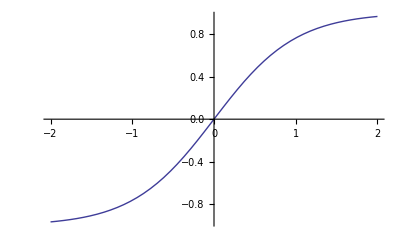

```mathematica
Manipulate[Plot[{((a^2-(ω+ΩS)^2) Tanh[1/2 √(a^2+(ω+ΩS)^2)])/(a^2+(ω+ΩS)^2),Tanh[ΩS]},{ΩS,-2,2}],
```